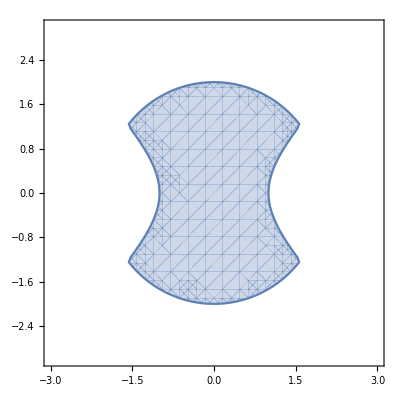

```mathematica
RegionPlot[Abs[x+I y]<2 && Re[(x+ I y)^2]≤ 1, {x,-3,3},{y,-3,3}]
```

```mathematica
ContourPlot[{Abs[x+I y]==2 , Re[(x+ I y)^2]== 1}, {x,-3,3},{y,-3,3}]
```

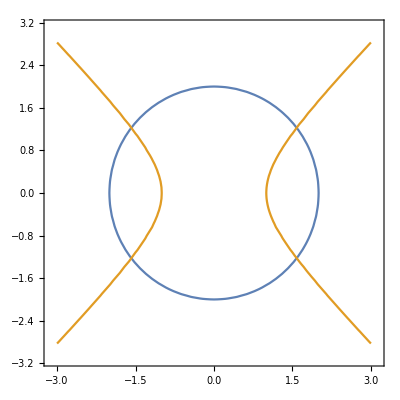

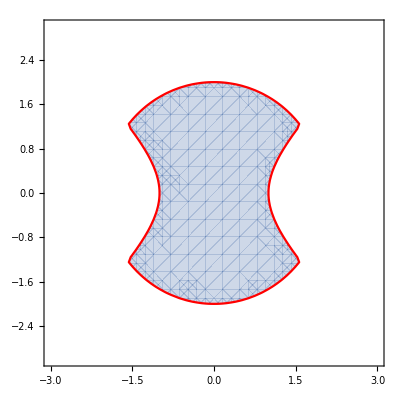

```mathematica
RegionPlot[Abs[x+I y]<2 && Re[(x+ I y)^2]≤ 1, {x,-3,3},{y,-3,3}, BoundaryStyle -> Directive[Red,Bold]]
```

```mathematica
g[z_]:=Log[z^3+1]
```

```mathematica
ParametricPlot3D[{x,y,Re[g[x+ I y]]},{x, -5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x,y,Arg[(x+I y)^3+1]},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

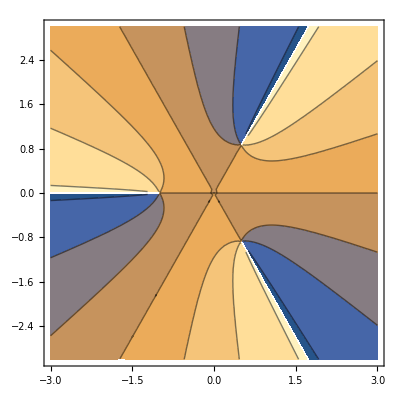

```mathematica
ContourPlot[Arg[(x+I y)^3+1],{x,-3,3},{y,-3,3}]
```

```mathematica
Exp[I Pi/3]
```

ⅇ^((ⅈ π)/3)

```mathematica
%^3
```

-1

```mathematica
%+1
```

0

```mathematica
p[k_]:=Plot3D[Arg[(x+I y)^3+1] + Pi*2*k,{x,-5,5},{y,-5,5}]
Show[p[-1],p[0],p[1],PlotRange->All]
```

-Graphics3D-